```mathematica
A30[p_, q_] = (-1594323+604800 π^2+4 p (1245184-713743 p+100800 (-3+2 p) π^2)-2854972 q^2+806400 π^2 q^2)/(345600 q);
```

```mathematica
B30[p_, q_] = -((2657205+4 p (-1507328+621593 p)+2486372 q^2)/(354816 q));
```

```mathematica
C30[p_, q_] =(1/(1058400 q))(-1594323+p (6209536-6879600 π^2)+28 p^2 (-145849+163800 π^2)-4083772 q^2+1146600 π^2 (3+4 q^2));
```

```mathematica
D30[p_, q_] = 3q/8;
```

```mathematica
F30[p_, q_] = 3q/8;
```

```mathematica
(* x in this code corresponds to alpha in the paper *)
L2[x_, p_, q_] = (A30[p, q]x^2 + 2B30[p, q]x + C30[p, q])/(D30[p, q]x^2 + F30[p, q])
```

1/((3 q)/8+(3 q x^2)/8)(1/(1058400 q)(-1594323+p (6209536-6879600 π^2)+28 p^2 (-145849+163800 π^2)-4083772 q^2+1146600 π^2 (3+4 q^2))-((2657205+4 p (-1507328+621593 p)+2486372 q^2) x)/(177408 q)+1/(345600 q)(-1594323+604800 π^2+4 p (1245184-713743 p+100800 (-3+2 p) π^2)-2854972 q^2+806400 π^2 q^2) x^2)

```mathematica
L1[x_, p_, q_] = Pi^2(1 + 1/q)^2
```

π^2 (1+1/q)^2

```mathematica
H[x_, p_, q_] = L2[x, p, q]/L1[x, p, q] // FullSimplify (* want to show this is ≤ 7/3 *)
```

-((718743872 q^2+3188646 (88+875 x)-28 p^2 (-25669424-7 x (13319850+7851173 x)+2217600 π^2 (13+7 x^2))+256 p (363825 π^2 (13+7 x^2)-1024 (4169+7 x (3450+1463 x)))+49 (-316800 π^2 (3+4 q^2) (13+7 x^2)+x (17537553 x+4 q^2 (13319850+7851173 x))))/(69854400 π^2 (1+q)^2 (1+x^2)))

```mathematica
Obj[x_, p_, q_] = 3*Numerator[H[x, p, q]] - 7*Denominator[H[x, p, q]] // FullSimplify (*want to show that this is ≤ 0 *)
```

3 (-718743872 q^2-2610690600 q^2 x-539 (1594323+2854972 q^2) x^2-3188646 (88+875 x)+7761600 π^2 (57-42 q+83 q^2+7 (3+q (-6+5 q)) x^2)+28 p^2 (-25669424-7 x (13319850+7851173 x)+2217600 π^2 (13+7 x^2))-256 p (363825 π^2 (13+7 x^2)-1024 (4169+7 x (3450+1463 x))))

```mathematica
(* Checking that this is a positive definite quadratic in each of p and q separately*)
quadp = SeriesCoefficient[Obj[x, p, q], {p, 0, 2}]
```

84 (-25669424-7 x (13319850+7851173 x)+2217600 π^2 (13+7 x^2))

```mathematica
Minimize[quadp, x] // N
```

{1.9886×10^10,{x→0.4745}}

```mathematica
quadq = SeriesCoefficient[Obj[x, p, q], {q, 0, 2}]
```

3 (-718743872-2610690600 x-1538829908 x^2+7761600 π^2 (83+35 x^2))

```mathematica
Minimize[quadq, x] // N
```

{1.24432×10^10,{x→1.14273}}

```mathematica
(* Proof when (p, q) = (0.65, 0.156) *)
PointObj[x_] = Obj[x, 65/100, 156/1000] // FullSimplify
```

(3 (6788089600688+7 x (1414193259450+1768358569901 x)-7761600 π^2 (312007+977515 x^2)))/62500

```mathematica
quad = SeriesCoefficient[PointObj[x], {x, 0, 2}];
lin = SeriesCoefficient[PointObj[x], {x, 0, 1}];
const = SeriesCoefficient[PointObj[x], {x, 0, 0}];
```

```mathematica
quad // N
```

-3.00014×10^9

```mathematica
lin^2 - 4 * quad * const // N
```

-9.6317×10^18

```mathematica
(* Proof for (p, 1.7p - 1.38) *)
(* First determining the range of values of p *)
Solve[17p/10 - 138/100 == 156/1000, p]
Solve[17p/10 - 138/100 == Sqrt[1/4 - (p - 1/2)^2], p]
```

{{p→384/425}}

{{p→(1423+10 √1729)/1945}}

```mathematica
pmin = 384/425;
pmax = (1423+10 √1729)/1945;
```

```mathematica
LineObj[x_, p_] = Obj[x, p, 17p/10 - 138/100] // FullSimplify
```

1/625 (528 (-5857161498+15856621390 p-9928670675 p^2+11025 (682563+5 p (-308418+171935 p)) π^2)-3150 (4620157398+5 p (-2211921178+1208998385 p)) x+1617 (-4394582298+11485165390 p-6941150675 p^2+126000 (10401+5 p (-4566+2245 p)) π^2) x^2)

```mathematica
quad = SeriesCoefficient[LineObj[x, p], {x, 0, 2}] // FullSimplify;
lin = SeriesCoefficient[LineObj[x, p], {x, 0, 1}] // FullSimplify;
const = SeriesCoefficient[LineObj[x, p], {x, 0, 0}] // FullSimplify;
disc = lin^2 - 4*quad*const // FullSimplify;
```

```mathematica
quad
```

1617/625 (-4394582298+11485165390 p-6941150675 p^2+126000 (10401+5 p (-4566+2245 p)) π^2)

```mathematica
Maximize[{quad, pmin ≤ p ≤ pmax}, p] // N
```

{-2.60188×10^9,{p→0.903529}}

```mathematica
disc
```

1/390625 1764 (5625 (4620157398+5 p (-2211921178+1208998385 p))^2-1936 (-4394582298+11485165390 p-6941150675 p^2+126000 (10401+5 p (-4566+2245 p)) π^2) (-5857161498+15856621390 p-9928670675 p^2+11025 (682563+5 p (-308418+171935 p)) π^2))

```mathematica
(* Differentiating twice to check that the discriminant is convex in p *)
doublederiv = Expand[D[D[disc, p], p]] // FullSimplify
```

1/15625 7056 (9729255420442511140432-19096331525875492404510 p+8655143124687404826075 p^2+4573800 (3014261595433359+10 p (-705658761345812+405487057694915 p)) π^2-8068183200000 (345394427+5 p (-147745362+77198815 p)) π^4)

```mathematica
Minimize[{doublederiv, pmin ≤ p ≤ pmax}, p] // N
```

{1.21487×10^21,{p→0.903529}}

```mathematica
(* So the discriminant is convex so we just need to evaluate it at the endpoints *)
disc /. p -> pmin // N
disc /. p -> pmax // N
```

-4.96593×10^17

-3.44375×10^17

```mathematica
(* Proof for (p, Sqrt[1/4 - (p - 1/2)^2]) with p in [0.65, pmax] *)
p1 = 65/100;
p2 = pmax;
```

```mathematica
SemicircleObj[x_, p_] = Obj[x, p, Sqrt[1/4 - (p - 1/2)^2]] // FullSimplify
```

27 (-177147 (22+7 x) (8+77 x)+236196 p (22+7 x) (8+77 x)+18110400 p^2 π^2 (1+x^2)-862400 p π^2 (73+49 x^2)-2587200 π^2 (-19+14 √(-(-1+p) p)+7 (-1+2 √(-(-1+p) p)) x^2))

```mathematica
F[p_] = 1/27 * SeriesCoefficient[SemicircleObj[x, p], {x, 0, 2}]
```

-95482233+127309644 p-42257600 p π^2+18110400 p^2 π^2-18110400 (-1+2 √(-(-1+p) p)) π^2

```mathematica
G[p_] = 1/27 * SeriesCoefficient[SemicircleObj[x, p], {x, 0, 0}]
```

-31177872+41570496 p-62955200 p π^2+18110400 p^2 π^2-2587200 (-19+14 √(-(-1+p) p)) π^2

```mathematica
(* Showing that f is negative on [p1, p2] *)
D[F[p], p]
```

127309644-42257600 π^2+36220800 p π^2-(18110400 (1-2 p) π^2)/(√(-(-1+p) p))

```mathematica
D[F[p], p] /. p -> p1
D[F[p], p] /. p -> p1 // N
```

127309644-18714080 π^2+15523200 √(7/13) π^2

5.50329×10^7

```mathematica
F[p] /. p -> p2
F[p] /. p -> p2 // N
```

-95482233+(127309644 (1423+10 √1729))/1945-8451520/389 (1423+10 √1729) π^2+(724416 (1423+10 √1729)^2 π^2)/151321-18110400 (-1+2 √(((1423+10 √1729) (1+(-1423-10 √1729)/1945))/1945)) π^2

-1.12135×10^8

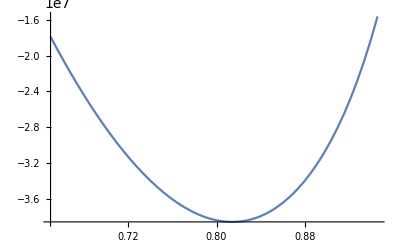

```mathematica
Plot[G[p], {p, p1, p2}]
```

```mathematica
(* COMPUTATIONS FOR g 
g(x) is given by -31177872+41570496 x-62955200 Pi^2 x+18110400 Pi^2 x^2-2587200 (-19+14 Sqrt[(1-x) x] Pi^2)
We may verify with WolframAlpha that g(x) has no zeros in [p1, p2], from which we may deduce that g(x) is negative in this interval (indeed, its only root is approximately 0.002).
The derivative of g(x) is given by
D[-31177872+41570496 x-62955200 Pi^2 x+18110400 Pi^2 x^2-2587200 (-19+14 Pi^2 Sqrt[(1-x) x]),x]
with output 
41570496-62955200 Pi^2+36220800 Pi^2 x-(18110400 Pi^2 (1-2 x))/Sqrt[(1-x) x]
We may verify with WolframAlpha that the only root of g'(x) in [p1, p2] is approximately 0.81416, which is easily seen to be the minimum value of g in that interval
*)
```

```mathematica
(* COMPUTATIONS FOR r, from which it follows that r is negative in [p1,p3] *)
f0[x_]:=-95482233+127309644x-42257600*Pi^2*x+18110400*Pi^2*x^2-18110400(-1+2(1/2-(x-1/2)^2-2/100))*Pi^2
```

```mathematica
g0[x_]:=-31177872+41570496x-62955200*Pi^2*x+18110400*Pi^2*x^2-2587200(-19+14(-2(x-1/2)^2+1/2))*Pi^2
```

```mathematica
r[x_]:=729(-310007250+413343000x)^2-2916*f0[x]*g0[x]
```

```mathematica
Expand[r[x]]
```

61379440735528381284+14575651214627365632 π^2-1401822174632140800 π^4-163678508628075683424 x-64267055186099141376 π^2 x+15110349613367500800 π^4 x+109119005752050455616 x^2+89928689951868768000 π^2 x^2-41354816828193792000 π^4 x^2-40202069150765491200 π^2 x^3+42173077768335360000 π^4 x^3-14346133366118400000 π^4 x^4

```mathematica
N[Roots[61379440735528381284+14575651214627365632 π^2-1401822174632140800 π^4-163678508628075683424 x-64267055186099141376 π^2 x+15110349613367500800 π^4 x+109119005752050455616 x^2+89928689951868768000 π^2 x^2-41354816828193792000 π^4 x^2-40202069150765491200 π^2 x^3+42173077768335360000 π^4 x^3-14346133366118400000 π^4 x^4==0,x]]
```

x==-0.0745624+4.12137×10^-17 ⅈ||x==0.614009-3.31644×10^-16 ⅈ||x==0.843425+3.79498×10^-16 ⅈ||x==1.27288-8.90678×10^-17 ⅈ